# 粒子群优化算法

### 函数图像



```mathematica
Plot[x^2,{x,-2,2}]
```

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
a=10;
Plot3D[20+Sum[x^2-a Cos[2π x],{x,{x1,x2}}],{x1,-5,5},{x2,-5,5},ColorFunction->Hue,Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot[20+Sum[x^2-a Cos[2π x],{x,{x1,x2}}],{x1,-5,5},{x2,-5,5}]
```

-Graphics-

```mathematica
FindMinimum[Sum[x^2-10 Cos[2π x],{x,{x1,x2}}],{{x1,3},{x2,3}},WorkingPrecision->30]
```

{-2.09079751702597872937274781811,{x1→2.98485570103948124686274356531,x2→2.98485570103948124686274356531}}

```mathematica
Minimize[Sum[x^2-10 Cos[2π x],{x,{x1,x2}}],{x1,x2}]
```

Minimize[x1^2+x2^2-10 Cos[2 π x1]-10 Cos[2 π x2],{x1,x2}]

## PSO实现

### 目标函数(适应度)

```mathematica
fitness[xn_]:=Sum[x^2-10Cos[2π x],{x,xn}]
```

### 测试fitness

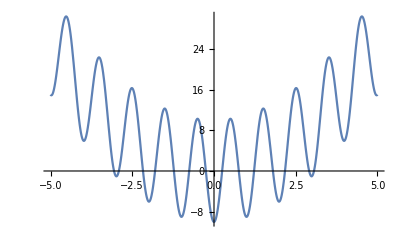

```mathematica
Plot[fitness[{x}],{x,-5,5}]
```

```mathematica
Plot3D[fitness[{x,y}],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Differences
```

### 初始化参数

```mathematica
init[]:=(ω=0.5;
c1=2;
c2=2;
r1=RandomReal[];
r2=RandomReal[];
α=1;

dimension=2;
num=50;
vMax=Table[1,dimension];
xMax=Table[5,dimension];
x=RandomReal[{-5,5},{num,dimension}];
v=RandomReal[{-1,1},{num,dimension}];
px=x;
pxF=fitness[#]&/@px;

pgF=Min[pxF];
pg=x[[PositionIndex[pxF][pgF][[1]]]];
iterNum=25;)
```

### 更新粒子

```mathematica
pso[]:=(
ax={x};
Do[v=ω v+c1 r1 (px-x)+c2 r2 (Table[pg,num]-x);
x=x+α v;
xF=fitness[#]&/@x;
AppendTo[ax,x];
Do[
If[xF[[r]]<pxF[[r]],
px[[r]]=x[[r]];pxF[[r]]=xF[[r]];
If[xF[[r]]<pgF,
pg=x[[r]];pgF=xF[[r]]]],
{r,num}],
iterNum])
```

### 计算

```mathematica
init[]
pso[]
{pg,pgF}
```

{{-0.0000859619,-0.00224058},-19.999}

```mathematica
cp=ContourPlot[fitness[{x,y}],{x,-5,5},{y,-5,5}];
lp[pts_]:=ListPlot[pts,PlotStyle->Directive[PointSize[Large],Magenta]];

Monitor[m=Table[Image@Show[cp,lp[ax[[i]]]],{i,iterNum}];ListAnimate[m],i]
```

```mathematica
Export["E:\\Mathematica\\pso.gif",m]
```

E:\Mathematica\pso.gif

```mathematica
l={3,9,2,5,4,8,7,0};
Max[l]
First@PositionIndex[l][Max[l]]
Position[l,9]
```

9

2

{{2}}